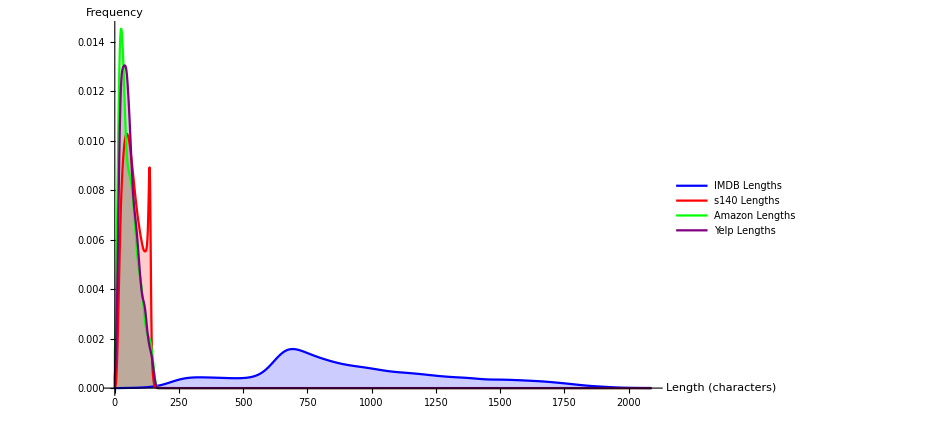

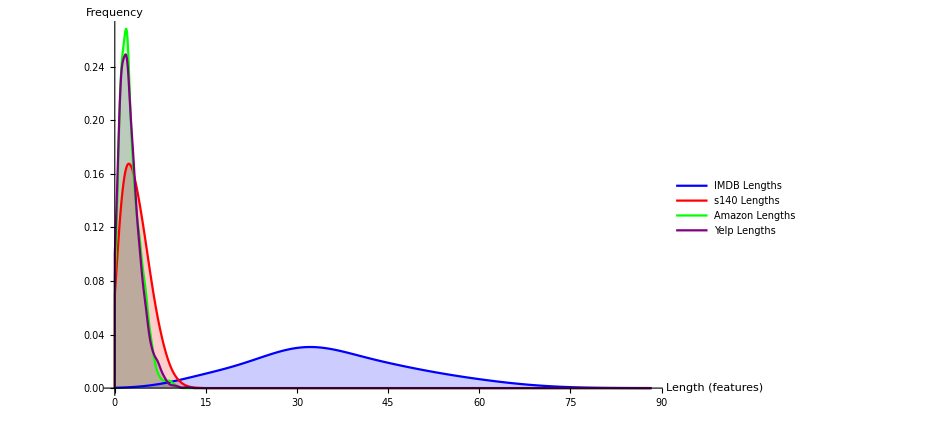

```mathematica
s140CLengths = Import["~/Downloads/s140_train_lengths.csv"][[1]];
imdbCLengths = Import["~/Downloads/imdb_train_lengths.csv"][[1]];
amazonCLengths = Import["~/Downloads/amazon_test_lengths.csv"][[1]];
yelpCLengths = Import["~/Downloads/yelp_test_lengths.csv"][[1]];

s140FLengths = Import["~/Downloads/s140_feature_lengths.csv"][[1]];
imdbFLengths = Import["~/Downloads/imdb_feature_lengths.csv"][[1]];
amazonFLengths = Import["~/Downloads/amazon_feature_lengths.csv"][[1]];
yelpFLengths = Import["~/Downloads/yelp_feature_lengths.csv"][[1]];

pltChars = SmoothHistogram[{imdbCLengths, s140CLengths, amazonCLengths, yelpCLengths}, ImageSize->700, PlotLegends->Placed[{"IMDB Lengths", "s140 Lengths", "Amazon Lengths", "Yelp Lengths"}, Above], Filling->Bottom, PlotRange->{{0, All}, {0, All}}, AxesLabel->{"Length (characters)", "Frequency"}, LabelStyle->Directive[14, Black], PlotStyle->{Directive[Blue,Thick, 14], Directive[Red,Thick, 14], Directive[Green,Thick, 14], Directive[Purple,Thick, 14]}]

pltFeatures = SmoothHistogram[{imdbFLengths, s140FLengths, amazonFLengths, yelpFLengths}, {"Standardized", 0.3}, ImageSize->700, PlotLegends->Placed[{"IMDB Lengths", "s140 Lengths", "Amazon Lengths", "Yelp Lengths"}, Above], Filling->Bottom, PlotRange->{{0, All}, {0, All}}, AxesLabel->{"Length (features)", "Frequency"}, LabelStyle->Directive[14, Black], PlotStyle->{Directive[Blue,Thick, 14], Directive[Red,Thick, 14], Directive[Green,Thick, 14], Directive[Purple,Thick, 14]}]
```

```mathematica
Export["~/Downloads/character_length_historgram.pdf",pltChars]
Export["~/Downloads/feature_length_historgram.pdf",pltFeatures]
```

~/Downloads/character_length_historgram.pdf

~/Downloads/feature_length_historgram.pdf